```mathematica
Q={{0,0},{0,4 π/3},{0,-4 π/3}}
```

{{0,0},{0,(4 π)/3},{0,-(4 π)/3}}

```mathematica
a=0*{0,-1}+0*{(√3)/2,-1/2}
```

{0,0}

```mathematica
b=-1*{0,-1}+1*{(√3)/2,-1/2}
```

{(√3)/2,1/2}

```mathematica
c=-2*{0,-1}+2*{(√3)/2,-1/2}
```

{√3,1}

```mathematica
H00=1/3Table[3*U1*Exp[-I*(q1-q2).a]+(U0+3*U1)Exp[-I*(q1-q2).b]+6*U1*Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]
```

{{1/3 (U0+12 U1),1/3 (3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+12 U1),1/3 (3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1))},{1/3 (3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+12 U1)}}

```mathematica
Eigenvalues[H00]//Simplify
```

{U0+3 U1,3 U1,6 U1}

```mathematica
Eigenvalues[H11]//Simplify
```

{U0+3 U1,3 U1,6 U1}

```mathematica
Collect[H00//Expand,{U0,U1}]//MatrixForm
```

(U0/3+4 U1 | 1/3 ⅇ^((2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | 1/3 ⅇ^(-(2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1
1/3 ⅇ^(-(2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1 | 1/3 ⅇ^((2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1
1/3 ⅇ^((2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | 1/3 ⅇ^(-(2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1)

```mathematica
H11=1/3Table[3*U1*Exp[-I*(q1-q2).b]+(U0+3*U1)Exp[-I*(q1-q2).a]+6*U1*Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]
```

{{1/3 (U0+12 U1),1/3 (U0+3 U1+3 ⅇ^(-(2 ⅈ π)/3) U1+6 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+3 ⅇ^((2 ⅈ π)/3) U1)},{1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+3 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+12 U1),1/3 (U0+3 U1+3 ⅇ^(-(2 ⅈ π)/3) U1+6 ⅇ^((2 ⅈ π)/3) U1)},{1/3 (U0+3 U1+3 ⅇ^(-(2 ⅈ π)/3) U1+6 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+3 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+12 U1)}}

```mathematica
Collect[H11//Expand,{U0,U1}]//MatrixForm
```

(U0/3+4 U1 | U0/3+(1+ⅇ^(-(2 ⅈ π)/3)+2 ⅇ^((2 ⅈ π)/3)) U1 | U0/3+(1+2 ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1
U0/3+(1+2 ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1 | U0/3+(1+ⅇ^(-(2 ⅈ π)/3)+2 ⅇ^((2 ⅈ π)/3)) U1
U0/3+(1+ⅇ^(-(2 ⅈ π)/3)+2 ⅇ^((2 ⅈ π)/3)) U1 | U0/3+(1+2 ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1)

```mathematica
Collect[H00//Expand,{U0,U1}]/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.796267 | -0.164283-0.0145204 ⅈ | -0.164283+0.0145204 ⅈ
-0.164283+0.0145204 ⅈ | 0.796267 | -0.164283-0.0145204 ⅈ
-0.164283-0.0145204 ⅈ | -0.164283+0.0145204 ⅈ | 0.796267)

```mathematica
Collect[H11//Expand,{U0,U1}]/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.796267 | 0.0947167+0.135013 ⅈ | 0.0947167-0.135013 ⅈ
0.0947167-0.135013 ⅈ | 0.796267 | 0.0947167+0.135013 ⅈ
0.0947167+0.135013 ⅈ | 0.0947167-0.135013 ⅈ | 0.796267)

```mathematica
Hfock00=1/3Table[(-U0)*Exp[-I*(q1-q2).a],{q1,Q},{q2,Q}]
```

{{-U0/3,-U0/3,-U0/3},{-U0/3,-U0/3,-U0/3},{-U0/3,-U0/3,-U0/3}}

```mathematica
Hfock11=1/3Table[(-U0)*Exp[-I*(q1-q2).b],{q1,Q},{q2,Q}]
```

{{-U0/3,-1/3 ⅇ^(-(2 ⅈ π)/3) U0,-1/3 ⅇ^((2 ⅈ π)/3) U0},{-1/3 ⅇ^((2 ⅈ π)/3) U0,-U0/3,-1/3 ⅇ^(-(2 ⅈ π)/3) U0},{-1/3 ⅇ^(-(2 ⅈ π)/3) U0,-1/3 ⅇ^((2 ⅈ π)/3) U0,-U0/3}}

```mathematica
Hfock00/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(-0.172667 | -0.172667 | -0.172667
-0.172667 | -0.172667 | -0.172667
-0.172667 | -0.172667 | -0.172667)

```mathematica
Hfock11/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(-0.172667 | 0.0863333+0.149534 ⅈ | 0.0863333-0.149534 ⅈ
0.0863333-0.149534 ⅈ | -0.172667 | 0.0863333+0.149534 ⅈ
0.0863333+0.149534 ⅈ | 0.0863333-0.149534 ⅈ | -0.172667)

```mathematica
Hhartree00=1/3Table[(3*U1+U0)*Exp[-I*(q1-q2).a]+(U0+3*U1)Exp[-I*(q1-q2).b]+6*U1*Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]
```

{{1/3 (2 U0+12 U1),1/3 (U0+3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1),1/3 (U0+3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1))},{1/3 (U0+3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1)}}

```mathematica
Hhartree11=1/3Table[(3*U1+U0)*Exp[-I*(q1-q2).b]+(U0+3*U1)Exp[-I*(q1-q2).a]+6*U1*Exp[-I*(q1-q2).c]{q1,Q},{q2,Q}]
```

{{1/3 (2 U0+12 U1),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1)}}

```mathematica
Hhartree00/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.968933 | -0.0167667+0. ⅈ | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | 0.968933 | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | -0.0167667+0. ⅈ | 0.968933)

```mathematica
Hhartree11/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.968933 | -0.0167667+0. ⅈ | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | 0.968933 | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | -0.0167667+0. ⅈ | 0.968933)

```mathematica
Eigenvalues[H00]/.{U0->0.5180,U1->0.1559}//Chop
```

{0.9857,0.4677,0.9354}

```mathematica
mA=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],{1,0,0}}])]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
mB=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[2 π/3],Sin[2 π/3],0}}])]
```

{{1/2,1/2 (-1/2+(ⅈ √3)/2)},{1/2 (-1/2-(ⅈ √3)/2),1/2}}

```mathematica
mC=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[4 π/3],Sin[4 π/3],0}}])]
```

{{1/2,1/2 (-1/2-(ⅈ √3)/2)},{1/2 (-1/2+(ⅈ √3)/2),1/2}}

```mathematica
Hartree00=1/3U0*Table[(mA[[1,1]]+mA[[2,2]])Exp[-I*(q1-q2).a]+(mB[[1,1]]+mB[[2,2]])Exp[-I*(q1-q2).b]+(mC[[1,1]]+mC[[2,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{U0,0,0},{0,U0,0},{0,0,U0}}

```mathematica
Hartree11=1/3U0*Table[(mA[[1,1]]+mA[[2,2]])Exp[-I*(q1-q2).a]+(mB[[1,1]]+mB[[2,2]])Exp[-I*(q1-q2).b]+(mC[[1,1]]+mC[[2,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify//Chop
```

{{U0,0,0},{0,U0,0},{0,0,U0}}

```mathematica
Fock00=1/3U0*Table[(mA[[1,1]])Exp[-I*(q1-q2).a]+(mB[[1,1]])Exp[-I*(q1-q2).b]+(mC[[1,1]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{U0/2,0,0},{0,U0/2,0},{0,0,U0/2}}

```mathematica
Fock01=1/3U0*Table[(mA[[2,1]])Exp[-I*(q1-q2).a]+(mB[[2,1]])Exp[-I*(q1-q2).b]+(mC[[2,1]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{0,U0/2,0},{0,0,U0/2},{U0/2,0,0}}

```mathematica
Fock11=1/3U0*Table[(mA[[2,2]])Exp[-I*(q1-q2).a]+(mB[[2,2]])Exp[-I*(q1-q2).b]+(mC[[2,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{U0/2,0,0},{0,U0/2,0},{0,0,U0/2}}

```mathematica
Fock10=1/3U0*Table[(mA[[1,2]])Exp[-I*(q1-q2).a]+(mB[[1,2]])Exp[-I*(q1-q2).b]+(mC[[1,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{0,0,U0/2},{U0/2,0,0},{0,U0/2,0}}

```mathematica
H=ArrayFlatten[{{Hartree00,0},{0,Hartree11}}]-ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}]//MatrixForm
```

(U0/2 | 0 | 0 | 0 | -U0/2 | 0
0 | U0/2 | 0 | 0 | 0 | -U0/2
0 | 0 | U0/2 | -U0/2 | 0 | 0
0 | 0 | -U0/2 | U0/2 | 0 | 0
-U0/2 | 0 | 0 | 0 | U0/2 | 0
0 | -U0/2 | 0 | 0 | 0 | U0/2)

```mathematica
ArrayFlatten[{{Hartree00,0},{0,Hartree11}}]//MatrixForm
```

(U0 | 0 | 0 | 0 | 0 | 0
0 | U0 | 0 | 0 | 0 | 0
0 | 0 | U0 | 0 | 0 | 0
0 | 0 | 0 | U0 | 0 | 0
0 | 0 | 0 | 0 | U0 | 0
0 | 0 | 0 | 0 | 0 | U0)

```mathematica
ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}]//MatrixForm
```

(U0/2 | 0 | 0 | 0 | U0/2 | 0
0 | U0/2 | 0 | 0 | 0 | U0/2
0 | 0 | U0/2 | U0/2 | 0 | 0
0 | 0 | U0/2 | U0/2 | 0 | 0
U0/2 | 0 | 0 | 0 | U0/2 | 0
0 | U0/2 | 0 | 0 | 0 | U0/2)

```mathematica
ave=Table[(mA)Exp[I*(q1-q2).a]+(mB)Exp[I*(q1-q2).b]+(mC)Exp[I*(q1-q2).c],{q1,Q},{q2,Q}]/3//Simplify
```

{{{{1/2,0},{0,1/2}},{{0,1/2},{0,0}},{{0,0},{1/2,0}}},{{{0,0},{1/2,0}},{{1/2,0},{0,1/2}},{{0,1/2},{0,0}}},{{{0,1/2},{0,0}},{{0,0},{1/2,0}},{{1/2,0},{0,1/2}}}}

```mathematica
ave//MatrixForm
```

((1/2 | 0
0 | 1/2) | (0 | 1/2
0 | 0) | (0 | 0
1/2 | 0)
(0 | 0
1/2 | 0) | (1/2 | 0
0 | 1/2) | (0 | 1/2
0 | 0)
(0 | 1/2
0 | 0) | (0 | 0
1/2 | 0) | (1/2 | 0
0 | 1/2))

```mathematica
ave//MatrixForm
```

((1/2 | ⅈ/(2 √3)
-ⅈ/(2 √3) | 1/2) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0)
(0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (1/2 | ⅈ/(2 √3)
-ⅈ/(2 √3) | 1/2) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0)
(0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (1/2 | ⅈ/(2 √3)
-ⅈ/(2 √3) | 1/2))

```mathematica
ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}]/.U0-> 0.4995//MatrixForm
```

(0.24975 | 0 | 0 | 0.-0.144193 ⅈ | 0.124875+0.0720966 ⅈ | 0.124875+0.0720966 ⅈ
0 | 0.24975 | 0 | 0.124875+0.0720966 ⅈ | 0.-0.144193 ⅈ | 0.124875+0.0720966 ⅈ
0 | 0 | 0.24975 | 0.124875+0.0720966 ⅈ | 0.124875+0.0720966 ⅈ | 0.-0.144193 ⅈ
0.+0.144193 ⅈ | 0.124875-0.0720966 ⅈ | 0.124875-0.0720966 ⅈ | 0.24975 | 0 | 0
0.124875-0.0720966 ⅈ | 0.+0.144193 ⅈ | 0.124875-0.0720966 ⅈ | 0 | 0.24975 | 0
0.124875-0.0720966 ⅈ | 0.124875-0.0720966 ⅈ | 0.+0.144193 ⅈ | 0 | 0 | 0.24975)

```mathematica
{mA,mB,mC}
```

{{{0.5,0.5},{0.5,0.5}},{{0.5,-0.25+0.433013 ⅈ},{-0.25-0.433013 ⅈ,0.5}},{{0.5,-0.25+0.433013 ⅈ},{-0.25-0.433013 ⅈ,0.5}}}

```mathematica
expqq=Table[Exp[I*(q1-q2).i],{i,{a,b,c}},{q1,Q},{q2,Q}]
```

{{{1,1,1},{1,1,1},{1,1,1}},{{1,ⅇ^((2 ⅈ π)/3),ⅇ^(-(2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3)},{ⅇ^((2 ⅈ π)/3),ⅇ^(-(2 ⅈ π)/3),1}},{{1,ⅇ^(-(2 ⅈ π)/3),ⅇ^((2 ⅈ π)/3)},{ⅇ^((2 ⅈ π)/3),1,ⅇ^(-(2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^((2 ⅈ π)/3),1}}}

```mathematica
expqq[[1]]
```

{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}}

```mathematica
expqq[[2]]//MatrixForm
```

(1 | ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | 1 | ⅇ^((2 ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3) | 1)

```mathematica
expqq[[3]]//MatrixForm
```

(1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | 1 | ⅇ^(-(2 ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3) | 1)

```mathematica
Q
```

{{0,0},{0,(4 π)/3},{0,-(4 π)/3}}

```mathematica
Exp[I*(4 π)/3]
```

ⅇ^(-(2 ⅈ π)/3)

```mathematica
0-4 π/3
```

-(4 π)/3

```mathematica
qq=Table[(q1-q2).i,{i,{a,b,c}},{q1,Q},{q2,Q}]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,-(4 π)/3,(4 π)/3},{(4 π)/3,0,(8 π)/3},{-(4 π)/3,-(8 π)/3,0}},{{0,-(2 π)/3,(2 π)/3},{(2 π)/3,0,(4 π)/3},{-(2 π)/3,-(4 π)/3,0}}}

```mathematica
qq[[2]]//N//MatrixForm
```

(0. | -4.18879 | 4.18879
4.18879 | 0. | 8.37758
-4.18879 | -8.37758 | 0.)

```mathematica
qq[[3]]//N//MatrixForm
```

(0. | -2.0944 | 2.0944
2.0944 | 0. | 4.18879
-2.0944 | -4.18879 | 0.)

```mathematica
c
```

{(√3)/2,1/2}

```mathematica
expqq[[3]]//N
```

{{1.,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ},{-0.5+0.866025 ⅈ,1.,-0.5-0.866025 ⅈ},{-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,1.}}

```mathematica
Q=Flatten[Table[i*2π{-1/√(3),-1}+j*2π{2/√3,0},{i,{0,1/3,2/3}},{j,{0,1/3,2/3}}],1]
```

{{0,0},{(4 π)/(3 √3),0},{(8 π)/(3 √3),0},{-(2 π)/(3 √3),-(2 π)/3},{(2 π)/(3 √3),-(2 π)/3},{(2 π)/(√3),-(2 π)/3},{-(4 π)/(3 √3),-(4 π)/3},{0,-(4 π)/3},{(4 π)/(3 √3),-(4 π)/3}}

```mathematica
r=Table[i[[1]]*{0,-1}+i[[2]]*{(√3)/2,-1/2},{i,{{0,0},{-2,1},{-4,2}}}]
```

{{0,0},{(√3)/2,3/2},{√3,3}}

```mathematica
mA=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],{1,0,0}}])]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
mB=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[2 π/3],Sin[2 π/3],0}}])]
```

{{1/2,1/2 (-1/2+(ⅈ √3)/2)},{1/2 (-1/2-(ⅈ √3)/2),1/2}}

```mathematica
mC=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[4 π/3],Sin[4 π/3],0}}])]
```

{{1/2,1/2 (-1/2-(ⅈ √3)/2)},{1/2 (-1/2+(ⅈ √3)/2),1/2}}

```mathematica
r[[1]]
```

{0,0}

```mathematica
Q
```

{{{0,0},{2/(3 √3),0},{4/(3 √3),0}},{{-1/(3 √3),-1/3},{1/(3 √3),-1/3},{1/(√3),-1/3}},{{-2/(3 √3),-2/3},{0,-2/3},{2/(3 √3),-2/3}}}

```mathematica
Hartree00=1/3Table[(U0(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[1]]]+(3U2(mA[[1,1]]+mA[[2,2]])+U0(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[2]]]+(3U2(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+U0(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]//Simplify
```

{{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2}}

```mathematica
Collect[Hartree00//Expand,{U0,U2}]//MatrixForm
```

(U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2)

```mathematica
Hartree11=1/3Table[(U0(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[1]]]+(3U2(mA[[1,1]]+mA[[2,2]])+U0(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[2]]]+(3U2(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+U0(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]//Simplify
```

{{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2}}

```mathematica
Collect[Hartree11//Expand,{U0,U2}]//MatrixForm
```

(U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2)

```mathematica
Fock01=1/3Table[(U0*mA[[2,1]]+3U2*mB[[2,1]]+3U2*mC[[2,1]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[2,1]]+U0*mB[[2,1]]+3U2*mC[[2,1]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[2,1]]+3U2*mB[[2,1]]+U0*mC[[2,1]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)}}

```mathematica
Fock10=1/3Table[(U0*mA[[1,2]]+3U2*mB[[1,2]]+3U2*mC[[1,2]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[1,2]]+U0*mB[[1,2]]+3U2*mC[[1,2]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[1,2]]+3U2*mB[[1,2]]+U0*mC[[1,2]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)}}

```mathematica
Fock00=1/3Table[(U0*mA[[1,1]]+3U2*mB[[1,1]]+3U2*mC[[1,1]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[1,1]]+U0*mB[[1,1]]+3U2*mC[[1,1]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[1,1]]+3U2*mB[[1,1]]+U0*mC[[1,1]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)}}

```mathematica
Fock11=1/3Table[(U0*mA[[2,2]]+3U2*mB[[2,2]]+3U2*mC[[2,2]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[2,2]]+U0*mB[[2,2]]+3U2*mC[[2,2]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[2,2]]+3U2*mB[[2,2]]+U0*mC[[2,2]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)}}

```mathematica
H=ArrayFlatten[{{Hartree00,0},{0,Hartree11}}]-ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}];
```

```mathematica
Eigenvalues[H]
```

{0,0,0,0,0,0,0,0,0,0,0,0,-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,1],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,2],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,3],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,4],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,5],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,6]}

```mathematica
Eigenvalues[H/.{U0->0.5230,U2->0}]//Chop//Sort
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.569,1.569,1.569}

```mathematica
Hartree00/.{U0->0.5230,U2->0.0833}//MatrixForm
```

(1.0228 | 0 | 0 | 0 | 0 | 1.0228 | 0 | 1.0228 | 0
0 | 1.0228 | 0 | 1.0228 | 0 | 0 | 0 | 0 | 1.0228
0 | 0 | 1.0228 | 0 | 1.0228 | 0 | 1.0228 | 0 | 0
0 | 1.0228 | 0 | 1.0228 | 0 | 0 | 0 | 0 | 1.0228
0 | 0 | 1.0228 | 0 | 1.0228 | 0 | 1.0228 | 0 | 0
1.0228 | 0 | 0 | 0 | 0 | 1.0228 | 0 | 1.0228 | 0
0 | 0 | 1.0228 | 0 | 1.0228 | 0 | 1.0228 | 0 | 0
1.0228 | 0 | 0 | 0 | 0 | 1.0228 | 0 | 1.0228 | 0
0 | 1.0228 | 0 | 1.0228 | 0 | 0 | 0 | 0 | 1.0228)

```mathematica
Eigenvalues[H]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,1/12 ⅇ^(-4 ⅈ) Root[2016 ⅇ^(8 ⅈ) U0^2 U2-1152 ⅇ^((25 ⅈ)/3) U0^2 U2+1728 ⅇ^((26 ⅈ)/3) U0^2 U2-4608 ⅇ^(9 ⅈ) U0^2 U2+3168 ⅇ^((28 ⅈ)/3) U0^2 U2-11520 ⅇ^((29 ⅈ)/3) U0^2 U2+1152 ⅇ^(10 ⅈ) U0^2 U2-9216 ⅇ^((31 ⅈ)/3) U0^2 U2+23040 ⅇ^((32 ⅈ)/3) U0^2 U2+4608 ⅇ^(11 ⅈ) U0^2 U2+42048 ⅇ^((34 ⅈ)/3) U0^2 U2+21888 ⅇ^((35 ⅈ)/3) U0^2 U2-146304 ⅇ^(12 ⅈ) U0^2 U2+21888 ⅇ^((37 ⅈ)/3) U0^2 U2+42048 ⅇ^((38 ⅈ)/3) U0^2 U2+4608 ⅇ^(13 ⅈ) U0^2 U2+23040 ⅇ^((40 ⅈ)/3) U0^2 U2-9216 ⅇ^((41 ⅈ)/3) U0^2 U2+1152 ⅇ^(14 ⅈ) U0^2 U2-11520 ⅇ^((43 ⅈ)/3) U0^2 U2+3168 ⅇ^((44 ⅈ)/3) U0^2 U2-4608 ⅇ^(15 ⅈ) U0^2 U2+1728 ⅇ^((46 ⅈ)/3) U0^2 U2-1152 ⅇ^((47 ⅈ)/3) U0^2 U2+2016 ⅇ^(16 ⅈ) U0^2 U2+6048 ⅇ^(8 ⅈ) U0 U2^2-3456 ⅇ^((25 ⅈ)/3) U0 U2^2+5184 ⅇ^((26 ⅈ)/3) U0 U2^2-13824 ⅇ^(9 ⅈ) U0 U2^2+9504 ⅇ^((28 ⅈ)/3) U0 U2^2-34560 ⅇ^((29 ⅈ)/3) U0 U2^2+3456 ⅇ^(10 ⅈ) U0 U2^2-27648 ⅇ^((31 ⅈ)/3) U0 U2^2+69120 ⅇ^((32 ⅈ)/3) U0 U2^2+13824 ⅇ^(11 ⅈ) U0 U2^2+126144 ⅇ^((34 ⅈ)/3) U0 U2^2+65664 ⅇ^((35 ⅈ)/3) U0 U2^2-438912 ⅇ^(12 ⅈ) U0 U2^2+65664 ⅇ^((37 ⅈ)/3) U0 U2^2+126144 ⅇ^((38 ⅈ)/3) U0 U2^2+13824 ⅇ^(13 ⅈ) U0 U2^2+69120 ⅇ^((40 ⅈ)/3) U0 U2^2-27648 ⅇ^((41 ⅈ)/3) U0 U2^2+3456 ⅇ^(14 ⅈ) U0 U2^2-34560 ⅇ^((43 ⅈ)/3) U0 U2^2+9504 ⅇ^((44 ⅈ)/3) U0 U2^2-13824 ⅇ^(15 ⅈ) U0 U2^2+5184 ⅇ^((46 ⅈ)/3) U0 U2^2-3456 ⅇ^((47 ⅈ)/3) U0 U2^2+6048 ⅇ^(16 ⅈ) U0 U2^2+4536 ⅇ^(8 ⅈ) U2^3-2592 ⅇ^((25 ⅈ)/3) U2^3+3888 ⅇ^((26 ⅈ)/3) U2^3-10368 ⅇ^(9 ⅈ) U2^3+7128 ⅇ^((28 ⅈ)/3) U2^3-25920 ⅇ^((29 ⅈ)/3) U2^3+2592 ⅇ^(10 ⅈ) U2^3-20736 ⅇ^((31 ⅈ)/3) U2^3+51840 ⅇ^((32 ⅈ)/3) U2^3+10368 ⅇ^(11 ⅈ) U2^3+94608 ⅇ^((34 ⅈ)/3) U2^3+49248 ⅇ^((35 ⅈ)/3) U2^3-329184 ⅇ^(12 ⅈ) U2^3+49248 ⅇ^((37 ⅈ)/3) U2^3+94608 ⅇ^((38 ⅈ)/3) U2^3+10368 ⅇ^(13 ⅈ) U2^3+51840 ⅇ^((40 ⅈ)/3) U2^3-20736 ⅇ^((41 ⅈ)/3) U2^3+2592 ⅇ^(14 ⅈ) U2^3-25920 ⅇ^((43 ⅈ)/3) U2^3+7128 ⅇ^((44 ⅈ)/3) U2^3-10368 ⅇ^(15 ⅈ) U2^3+3888 ⅇ^((46 ⅈ)/3) U2^3-2592 ⅇ^((47 ⅈ)/3) U2^3+4536 ⅇ^(16 ⅈ) U2^3+(-80 ⅇ^(6 ⅈ) U0^2-16 ⅇ^((19 ⅈ)/3) U0^2-112 ⅇ^((20 ⅈ)/3) U0^2-48 ⅇ^(7 ⅈ) U0^2-224 ⅇ^((22 ⅈ)/3) U0^2-80 ⅇ^((23 ⅈ)/3) U0^2+1120 ⅇ^(8 ⅈ) U0^2-80 ⅇ^((25 ⅈ)/3) U0^2-224 ⅇ^((26 ⅈ)/3) U0^2-48 ⅇ^(9 ⅈ) U0^2-112 ⅇ^((28 ⅈ)/3) U0^2-16 ⅇ^((29 ⅈ)/3) U0^2-80 ⅇ^(10 ⅈ) U0^2-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-456 ⅇ^(6 ⅈ) U0 U2-264 ⅇ^((19 ⅈ)/3) U0 U2-1272 ⅇ^((20 ⅈ)/3) U0 U2-792 ⅇ^(7 ⅈ) U0 U2-1824 ⅇ^((22 ⅈ)/3) U0 U2-1320 ⅇ^((23 ⅈ)/3) U0 U2+13008 ⅇ^(8 ⅈ) U0 U2-1320 ⅇ^((25 ⅈ)/3) U0 U2-1824 ⅇ^((26 ⅈ)/3) U0 U2-792 ⅇ^(9 ⅈ) U0 U2-1272 ⅇ^((28 ⅈ)/3) U0 U2-264 ⅇ^((29 ⅈ)/3) U0 U2-456 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-504 ⅇ^(6 ⅈ) U2^2-360 ⅇ^((19 ⅈ)/3) U2^2-1656 ⅇ^((20 ⅈ)/3) U2^2-1080 ⅇ^(7 ⅈ) U2^2-2232 ⅇ^((22 ⅈ)/3) U2^2-1800 ⅇ^((23 ⅈ)/3) U2^2+16992 ⅇ^(8 ⅈ) U2^2-1800 ⅇ^((25 ⅈ)/3) U2^2-2232 ⅇ^((26 ⅈ)/3) U2^2-1080 ⅇ^(9 ⅈ) U2^2-1656 ⅇ^((28 ⅈ)/3) U2^2-360 ⅇ^((29 ⅈ)/3) U2^2-504 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(2 ⅇ^(2 ⅈ) U0+2 ⅇ^((8 ⅈ)/3) U0+4 ⅇ^((10 ⅈ)/3) U0-70 ⅇ^(4 ⅈ) U0+4 ⅇ^((14 ⅈ)/3) U0+2 ⅇ^((16 ⅈ)/3) U0+2 ⅇ^(6 ⅈ) U0-6 ⅇ^(2 ⅈ) U2-6 ⅇ^((8 ⅈ)/3) U2-12 ⅇ^((10 ⅈ)/3) U2-276 ⅇ^(4 ⅈ) U2-12 ⅇ^((14 ⅈ)/3) U2-6 ⅇ^((16 ⅈ)/3) U2-6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,1],1/12 ⅇ^(-4 ⅈ) Root[2016 ⅇ^(8 ⅈ) U0^2 U2-1152 ⅇ^((25 ⅈ)/3) U0^2 U2+1728 ⅇ^((26 ⅈ)/3) U0^2 U2-4608 ⅇ^(9 ⅈ) U0^2 U2+3168 ⅇ^((28 ⅈ)/3) U0^2 U2-11520 ⅇ^((29 ⅈ)/3) U0^2 U2+1152 ⅇ^(10 ⅈ) U0^2 U2-9216 ⅇ^((31 ⅈ)/3) U0^2 U2+23040 ⅇ^((32 ⅈ)/3) U0^2 U2+4608 ⅇ^(11 ⅈ) U0^2 U2+42048 ⅇ^((34 ⅈ)/3) U0^2 U2+21888 ⅇ^((35 ⅈ)/3) U0^2 U2-146304 ⅇ^(12 ⅈ) U0^2 U2+21888 ⅇ^((37 ⅈ)/3) U0^2 U2+42048 ⅇ^((38 ⅈ)/3) U0^2 U2+4608 ⅇ^(13 ⅈ) U0^2 U2+23040 ⅇ^((40 ⅈ)/3) U0^2 U2-9216 ⅇ^((41 ⅈ)/3) U0^2 U2+1152 ⅇ^(14 ⅈ) U0^2 U2-11520 ⅇ^((43 ⅈ)/3) U0^2 U2+3168 ⅇ^((44 ⅈ)/3) U0^2 U2-4608 ⅇ^(15 ⅈ) U0^2 U2+1728 ⅇ^((46 ⅈ)/3) U0^2 U2-1152 ⅇ^((47 ⅈ)/3) U0^2 U2+2016 ⅇ^(16 ⅈ) U0^2 U2+6048 ⅇ^(8 ⅈ) U0 U2^2-3456 ⅇ^((25 ⅈ)/3) U0 U2^2+5184 ⅇ^((26 ⅈ)/3) U0 U2^2-13824 ⅇ^(9 ⅈ) U0 U2^2+9504 ⅇ^((28 ⅈ)/3) U0 U2^2-34560 ⅇ^((29 ⅈ)/3) U0 U2^2+3456 ⅇ^(10 ⅈ) U0 U2^2-27648 ⅇ^((31 ⅈ)/3) U0 U2^2+69120 ⅇ^((32 ⅈ)/3) U0 U2^2+13824 ⅇ^(11 ⅈ) U0 U2^2+126144 ⅇ^((34 ⅈ)/3) U0 U2^2+65664 ⅇ^((35 ⅈ)/3) U0 U2^2-438912 ⅇ^(12 ⅈ) U0 U2^2+65664 ⅇ^((37 ⅈ)/3) U0 U2^2+126144 ⅇ^((38 ⅈ)/3) U0 U2^2+13824 ⅇ^(13 ⅈ) U0 U2^2+69120 ⅇ^((40 ⅈ)/3) U0 U2^2-27648 ⅇ^((41 ⅈ)/3) U0 U2^2+3456 ⅇ^(14 ⅈ) U0 U2^2-34560 ⅇ^((43 ⅈ)/3) U0 U2^2+9504 ⅇ^((44 ⅈ)/3) U0 U2^2-13824 ⅇ^(15 ⅈ) U0 U2^2+5184 ⅇ^((46 ⅈ)/3) U0 U2^2-3456 ⅇ^((47 ⅈ)/3) U0 U2^2+6048 ⅇ^(16 ⅈ) U0 U2^2+4536 ⅇ^(8 ⅈ) U2^3-2592 ⅇ^((25 ⅈ)/3) U2^3+3888 ⅇ^((26 ⅈ)/3) U2^3-10368 ⅇ^(9 ⅈ) U2^3+7128 ⅇ^((28 ⅈ)/3) U2^3-25920 ⅇ^((29 ⅈ)/3) U2^3+2592 ⅇ^(10 ⅈ) U2^3-20736 ⅇ^((31 ⅈ)/3) U2^3+51840 ⅇ^((32 ⅈ)/3) U2^3+10368 ⅇ^(11 ⅈ) U2^3+94608 ⅇ^((34 ⅈ)/3) U2^3+49248 ⅇ^((35 ⅈ)/3) U2^3-329184 ⅇ^(12 ⅈ) U2^3+49248 ⅇ^((37 ⅈ)/3) U2^3+94608 ⅇ^((38 ⅈ)/3) U2^3+10368 ⅇ^(13 ⅈ) U2^3+51840 ⅇ^((40 ⅈ)/3) U2^3-20736 ⅇ^((41 ⅈ)/3) U2^3+2592 ⅇ^(14 ⅈ) U2^3-25920 ⅇ^((43 ⅈ)/3) U2^3+7128 ⅇ^((44 ⅈ)/3) U2^3-10368 ⅇ^(15 ⅈ) U2^3+3888 ⅇ^((46 ⅈ)/3) U2^3-2592 ⅇ^((47 ⅈ)/3) U2^3+4536 ⅇ^(16 ⅈ) U2^3+(-80 ⅇ^(6 ⅈ) U0^2-16 ⅇ^((19 ⅈ)/3) U0^2-112 ⅇ^((20 ⅈ)/3) U0^2-48 ⅇ^(7 ⅈ) U0^2-224 ⅇ^((22 ⅈ)/3) U0^2-80 ⅇ^((23 ⅈ)/3) U0^2+1120 ⅇ^(8 ⅈ) U0^2-80 ⅇ^((25 ⅈ)/3) U0^2-224 ⅇ^((26 ⅈ)/3) U0^2-48 ⅇ^(9 ⅈ) U0^2-112 ⅇ^((28 ⅈ)/3) U0^2-16 ⅇ^((29 ⅈ)/3) U0^2-80 ⅇ^(10 ⅈ) U0^2-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-456 ⅇ^(6 ⅈ) U0 U2-264 ⅇ^((19 ⅈ)/3) U0 U2-1272 ⅇ^((20 ⅈ)/3) U0 U2-792 ⅇ^(7 ⅈ) U0 U2-1824 ⅇ^((22 ⅈ)/3) U0 U2-1320 ⅇ^((23 ⅈ)/3) U0 U2+13008 ⅇ^(8 ⅈ) U0 U2-1320 ⅇ^((25 ⅈ)/3) U0 U2-1824 ⅇ^((26 ⅈ)/3) U0 U2-792 ⅇ^(9 ⅈ) U0 U2-1272 ⅇ^((28 ⅈ)/3) U0 U2-264 ⅇ^((29 ⅈ)/3) U0 U2-456 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-504 ⅇ^(6 ⅈ) U2^2-360 ⅇ^((19 ⅈ)/3) U2^2-1656 ⅇ^((20 ⅈ)/3) U2^2-1080 ⅇ^(7 ⅈ) U2^2-2232 ⅇ^((22 ⅈ)/3) U2^2-1800 ⅇ^((23 ⅈ)/3) U2^2+16992 ⅇ^(8 ⅈ) U2^2-1800 ⅇ^((25 ⅈ)/3) U2^2-2232 ⅇ^((26 ⅈ)/3) U2^2-1080 ⅇ^(9 ⅈ) U2^2-1656 ⅇ^((28 ⅈ)/3) U2^2-360 ⅇ^((29 ⅈ)/3) U2^2-504 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(2 ⅇ^(2 ⅈ) U0+2 ⅇ^((8 ⅈ)/3) U0+4 ⅇ^((10 ⅈ)/3) U0-70 ⅇ^(4 ⅈ) U0+4 ⅇ^((14 ⅈ)/3) U0+2 ⅇ^((16 ⅈ)/3) U0+2 ⅇ^(6 ⅈ) U0-6 ⅇ^(2 ⅈ) U2-6 ⅇ^((8 ⅈ)/3) U2-12 ⅇ^((10 ⅈ)/3) U2-276 ⅇ^(4 ⅈ) U2-12 ⅇ^((14 ⅈ)/3) U2-6 ⅇ^((16 ⅈ)/3) U2-6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,2],1/12 ⅇ^(-4 ⅈ) Root[2016 ⅇ^(8 ⅈ) U0^2 U2-1152 ⅇ^((25 ⅈ)/3) U0^2 U2+1728 ⅇ^((26 ⅈ)/3) U0^2 U2-4608 ⅇ^(9 ⅈ) U0^2 U2+3168 ⅇ^((28 ⅈ)/3) U0^2 U2-11520 ⅇ^((29 ⅈ)/3) U0^2 U2+1152 ⅇ^(10 ⅈ) U0^2 U2-9216 ⅇ^((31 ⅈ)/3) U0^2 U2+23040 ⅇ^((32 ⅈ)/3) U0^2 U2+4608 ⅇ^(11 ⅈ) U0^2 U2+42048 ⅇ^((34 ⅈ)/3) U0^2 U2+21888 ⅇ^((35 ⅈ)/3) U0^2 U2-146304 ⅇ^(12 ⅈ) U0^2 U2+21888 ⅇ^((37 ⅈ)/3) U0^2 U2+42048 ⅇ^((38 ⅈ)/3) U0^2 U2+4608 ⅇ^(13 ⅈ) U0^2 U2+23040 ⅇ^((40 ⅈ)/3) U0^2 U2-9216 ⅇ^((41 ⅈ)/3) U0^2 U2+1152 ⅇ^(14 ⅈ) U0^2 U2-11520 ⅇ^((43 ⅈ)/3) U0^2 U2+3168 ⅇ^((44 ⅈ)/3) U0^2 U2-4608 ⅇ^(15 ⅈ) U0^2 U2+1728 ⅇ^((46 ⅈ)/3) U0^2 U2-1152 ⅇ^((47 ⅈ)/3) U0^2 U2+2016 ⅇ^(16 ⅈ) U0^2 U2+6048 ⅇ^(8 ⅈ) U0 U2^2-3456 ⅇ^((25 ⅈ)/3) U0 U2^2+5184 ⅇ^((26 ⅈ)/3) U0 U2^2-13824 ⅇ^(9 ⅈ) U0 U2^2+9504 ⅇ^((28 ⅈ)/3) U0 U2^2-34560 ⅇ^((29 ⅈ)/3) U0 U2^2+3456 ⅇ^(10 ⅈ) U0 U2^2-27648 ⅇ^((31 ⅈ)/3) U0 U2^2+69120 ⅇ^((32 ⅈ)/3) U0 U2^2+13824 ⅇ^(11 ⅈ) U0 U2^2+126144 ⅇ^((34 ⅈ)/3) U0 U2^2+65664 ⅇ^((35 ⅈ)/3) U0 U2^2-438912 ⅇ^(12 ⅈ) U0 U2^2+65664 ⅇ^((37 ⅈ)/3) U0 U2^2+126144 ⅇ^((38 ⅈ)/3) U0 U2^2+13824 ⅇ^(13 ⅈ) U0 U2^2+69120 ⅇ^((40 ⅈ)/3) U0 U2^2-27648 ⅇ^((41 ⅈ)/3) U0 U2^2+3456 ⅇ^(14 ⅈ) U0 U2^2-34560 ⅇ^((43 ⅈ)/3) U0 U2^2+9504 ⅇ^((44 ⅈ)/3) U0 U2^2-13824 ⅇ^(15 ⅈ) U0 U2^2+5184 ⅇ^((46 ⅈ)/3) U0 U2^2-3456 ⅇ^((47 ⅈ)/3) U0 U2^2+6048 ⅇ^(16 ⅈ) U0 U2^2+4536 ⅇ^(8 ⅈ) U2^3-2592 ⅇ^((25 ⅈ)/3) U2^3+3888 ⅇ^((26 ⅈ)/3) U2^3-10368 ⅇ^(9 ⅈ) U2^3+7128 ⅇ^((28 ⅈ)/3) U2^3-25920 ⅇ^((29 ⅈ)/3) U2^3+2592 ⅇ^(10 ⅈ) U2^3-20736 ⅇ^((31 ⅈ)/3) U2^3+51840 ⅇ^((32 ⅈ)/3) U2^3+10368 ⅇ^(11 ⅈ) U2^3+94608 ⅇ^((34 ⅈ)/3) U2^3+49248 ⅇ^((35 ⅈ)/3) U2^3-329184 ⅇ^(12 ⅈ) U2^3+49248 ⅇ^((37 ⅈ)/3) U2^3+94608 ⅇ^((38 ⅈ)/3) U2^3+10368 ⅇ^(13 ⅈ) U2^3+51840 ⅇ^((40 ⅈ)/3) U2^3-20736 ⅇ^((41 ⅈ)/3) U2^3+2592 ⅇ^(14 ⅈ) U2^3-25920 ⅇ^((43 ⅈ)/3) U2^3+7128 ⅇ^((44 ⅈ)/3) U2^3-10368 ⅇ^(15 ⅈ) U2^3+3888 ⅇ^((46 ⅈ)/3) U2^3-2592 ⅇ^((47 ⅈ)/3) U2^3+4536 ⅇ^(16 ⅈ) U2^3+(-80 ⅇ^(6 ⅈ) U0^2-16 ⅇ^((19 ⅈ)/3) U0^2-112 ⅇ^((20 ⅈ)/3) U0^2-48 ⅇ^(7 ⅈ) U0^2-224 ⅇ^((22 ⅈ)/3) U0^2-80 ⅇ^((23 ⅈ)/3) U0^2+1120 ⅇ^(8 ⅈ) U0^2-80 ⅇ^((25 ⅈ)/3) U0^2-224 ⅇ^((26 ⅈ)/3) U0^2-48 ⅇ^(9 ⅈ) U0^2-112 ⅇ^((28 ⅈ)/3) U0^2-16 ⅇ^((29 ⅈ)/3) U0^2-80 ⅇ^(10 ⅈ) U0^2-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-456 ⅇ^(6 ⅈ) U0 U2-264 ⅇ^((19 ⅈ)/3) U0 U2-1272 ⅇ^((20 ⅈ)/3) U0 U2-792 ⅇ^(7 ⅈ) U0 U2-1824 ⅇ^((22 ⅈ)/3) U0 U2-1320 ⅇ^((23 ⅈ)/3) U0 U2+13008 ⅇ^(8 ⅈ) U0 U2-1320 ⅇ^((25 ⅈ)/3) U0 U2-1824 ⅇ^((26 ⅈ)/3) U0 U2-792 ⅇ^(9 ⅈ) U0 U2-1272 ⅇ^((28 ⅈ)/3) U0 U2-264 ⅇ^((29 ⅈ)/3) U0 U2-456 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-504 ⅇ^(6 ⅈ) U2^2-360 ⅇ^((19 ⅈ)/3) U2^2-1656 ⅇ^((20 ⅈ)/3) U2^2-1080 ⅇ^(7 ⅈ) U2^2-2232 ⅇ^((22 ⅈ)/3) U2^2-1800 ⅇ^((23 ⅈ)/3) U2^2+16992 ⅇ^(8 ⅈ) U2^2-1800 ⅇ^((25 ⅈ)/3) U2^2-2232 ⅇ^((26 ⅈ)/3) U2^2-1080 ⅇ^(9 ⅈ) U2^2-1656 ⅇ^((28 ⅈ)/3) U2^2-360 ⅇ^((29 ⅈ)/3) U2^2-504 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(2 ⅇ^(2 ⅈ) U0+2 ⅇ^((8 ⅈ)/3) U0+4 ⅇ^((10 ⅈ)/3) U0-70 ⅇ^(4 ⅈ) U0+4 ⅇ^((14 ⅈ)/3) U0+2 ⅇ^((16 ⅈ)/3) U0+2 ⅇ^(6 ⅈ) U0-6 ⅇ^(2 ⅈ) U2-6 ⅇ^((8 ⅈ)/3) U2-12 ⅇ^((10 ⅈ)/3) U2-276 ⅇ^(4 ⅈ) U2-12 ⅇ^((14 ⅈ)/3) U2-6 ⅇ^((16 ⅈ)/3) U2-6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,3],1/12 ⅇ^(-4 ⅈ) Root[9072 ⅇ^(8 ⅈ) U0 U2^2-5184 ⅇ^((25 ⅈ)/3) U0 U2^2+7776 ⅇ^((26 ⅈ)/3) U0 U2^2-20736 ⅇ^(9 ⅈ) U0 U2^2+14256 ⅇ^((28 ⅈ)/3) U0 U2^2-51840 ⅇ^((29 ⅈ)/3) U0 U2^2+5184 ⅇ^(10 ⅈ) U0 U2^2-41472 ⅇ^((31 ⅈ)/3) U0 U2^2+103680 ⅇ^((32 ⅈ)/3) U0 U2^2+20736 ⅇ^(11 ⅈ) U0 U2^2+189216 ⅇ^((34 ⅈ)/3) U0 U2^2+98496 ⅇ^((35 ⅈ)/3) U0 U2^2-658368 ⅇ^(12 ⅈ) U0 U2^2+98496 ⅇ^((37 ⅈ)/3) U0 U2^2+189216 ⅇ^((38 ⅈ)/3) U0 U2^2+20736 ⅇ^(13 ⅈ) U0 U2^2+103680 ⅇ^((40 ⅈ)/3) U0 U2^2-41472 ⅇ^((41 ⅈ)/3) U0 U2^2+5184 ⅇ^(14 ⅈ) U0 U2^2-51840 ⅇ^((43 ⅈ)/3) U0 U2^2+14256 ⅇ^((44 ⅈ)/3) U0 U2^2-20736 ⅇ^(15 ⅈ) U0 U2^2+7776 ⅇ^((46 ⅈ)/3) U0 U2^2-5184 ⅇ^((47 ⅈ)/3) U0 U2^2+9072 ⅇ^(16 ⅈ) U0 U2^2+13608 ⅇ^(8 ⅈ) U2^3-7776 ⅇ^((25 ⅈ)/3) U2^3+11664 ⅇ^((26 ⅈ)/3) U2^3-31104 ⅇ^(9 ⅈ) U2^3+21384 ⅇ^((28 ⅈ)/3) U2^3-77760 ⅇ^((29 ⅈ)/3) U2^3+7776 ⅇ^(10 ⅈ) U2^3-62208 ⅇ^((31 ⅈ)/3) U2^3+155520 ⅇ^((32 ⅈ)/3) U2^3+31104 ⅇ^(11 ⅈ) U2^3+283824 ⅇ^((34 ⅈ)/3) U2^3+147744 ⅇ^((35 ⅈ)/3) U2^3-987552 ⅇ^(12 ⅈ) U2^3+147744 ⅇ^((37 ⅈ)/3) U2^3+283824 ⅇ^((38 ⅈ)/3) U2^3+31104 ⅇ^(13 ⅈ) U2^3+155520 ⅇ^((40 ⅈ)/3) U2^3-62208 ⅇ^((41 ⅈ)/3) U2^3+7776 ⅇ^(14 ⅈ) U2^3-77760 ⅇ^((43 ⅈ)/3) U2^3+21384 ⅇ^((44 ⅈ)/3) U2^3-31104 ⅇ^(15 ⅈ) U2^3+11664 ⅇ^((46 ⅈ)/3) U2^3-7776 ⅇ^((47 ⅈ)/3) U2^3+13608 ⅇ^(16 ⅈ) U2^3+(-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-216 ⅇ^(6 ⅈ) U0 U2-216 ⅇ^((19 ⅈ)/3) U0 U2-936 ⅇ^((20 ⅈ)/3) U0 U2-648 ⅇ^(7 ⅈ) U0 U2-1152 ⅇ^((22 ⅈ)/3) U0 U2-1080 ⅇ^((23 ⅈ)/3) U0 U2+9648 ⅇ^(8 ⅈ) U0 U2-1080 ⅇ^((25 ⅈ)/3) U0 U2-1152 ⅇ^((26 ⅈ)/3) U0 U2-648 ⅇ^(9 ⅈ) U0 U2-936 ⅇ^((28 ⅈ)/3) U0 U2-216 ⅇ^((29 ⅈ)/3) U0 U2-216 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-1944 ⅇ^(6 ⅈ) U2^2-648 ⅇ^((19 ⅈ)/3) U2^2-3672 ⅇ^((20 ⅈ)/3) U2^2-1944 ⅇ^(7 ⅈ) U2^2-6264 ⅇ^((22 ⅈ)/3) U2^2-3240 ⅇ^((23 ⅈ)/3) U2^2+37152 ⅇ^(8 ⅈ) U2^2-3240 ⅇ^((25 ⅈ)/3) U2^2-6264 ⅇ^((26 ⅈ)/3) U2^2-1944 ⅇ^(9 ⅈ) U2^2-3672 ⅇ^((28 ⅈ)/3) U2^2-648 ⅇ^((29 ⅈ)/3) U2^2-1944 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(-2 ⅇ^(2 ⅈ) U0-2 ⅇ^((8 ⅈ)/3) U0-4 ⅇ^((10 ⅈ)/3) U0-38 ⅇ^(4 ⅈ) U0-4 ⅇ^((14 ⅈ)/3) U0-2 ⅇ^((16 ⅈ)/3) U0-2 ⅇ^(6 ⅈ) U0+6 ⅇ^(2 ⅈ) U2+6 ⅇ^((8 ⅈ)/3) U2+12 ⅇ^((10 ⅈ)/3) U2-372 ⅇ^(4 ⅈ) U2+12 ⅇ^((14 ⅈ)/3) U2+6 ⅇ^((16 ⅈ)/3) U2+6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,1],1/12 ⅇ^(-4 ⅈ) Root[9072 ⅇ^(8 ⅈ) U0 U2^2-5184 ⅇ^((25 ⅈ)/3) U0 U2^2+7776 ⅇ^((26 ⅈ)/3) U0 U2^2-20736 ⅇ^(9 ⅈ) U0 U2^2+14256 ⅇ^((28 ⅈ)/3) U0 U2^2-51840 ⅇ^((29 ⅈ)/3) U0 U2^2+5184 ⅇ^(10 ⅈ) U0 U2^2-41472 ⅇ^((31 ⅈ)/3) U0 U2^2+103680 ⅇ^((32 ⅈ)/3) U0 U2^2+20736 ⅇ^(11 ⅈ) U0 U2^2+189216 ⅇ^((34 ⅈ)/3) U0 U2^2+98496 ⅇ^((35 ⅈ)/3) U0 U2^2-658368 ⅇ^(12 ⅈ) U0 U2^2+98496 ⅇ^((37 ⅈ)/3) U0 U2^2+189216 ⅇ^((38 ⅈ)/3) U0 U2^2+20736 ⅇ^(13 ⅈ) U0 U2^2+103680 ⅇ^((40 ⅈ)/3) U0 U2^2-41472 ⅇ^((41 ⅈ)/3) U0 U2^2+5184 ⅇ^(14 ⅈ) U0 U2^2-51840 ⅇ^((43 ⅈ)/3) U0 U2^2+14256 ⅇ^((44 ⅈ)/3) U0 U2^2-20736 ⅇ^(15 ⅈ) U0 U2^2+7776 ⅇ^((46 ⅈ)/3) U0 U2^2-5184 ⅇ^((47 ⅈ)/3) U0 U2^2+9072 ⅇ^(16 ⅈ) U0 U2^2+13608 ⅇ^(8 ⅈ) U2^3-7776 ⅇ^((25 ⅈ)/3) U2^3+11664 ⅇ^((26 ⅈ)/3) U2^3-31104 ⅇ^(9 ⅈ) U2^3+21384 ⅇ^((28 ⅈ)/3) U2^3-77760 ⅇ^((29 ⅈ)/3) U2^3+7776 ⅇ^(10 ⅈ) U2^3-62208 ⅇ^((31 ⅈ)/3) U2^3+155520 ⅇ^((32 ⅈ)/3) U2^3+31104 ⅇ^(11 ⅈ) U2^3+283824 ⅇ^((34 ⅈ)/3) U2^3+147744 ⅇ^((35 ⅈ)/3) U2^3-987552 ⅇ^(12 ⅈ) U2^3+147744 ⅇ^((37 ⅈ)/3) U2^3+283824 ⅇ^((38 ⅈ)/3) U2^3+31104 ⅇ^(13 ⅈ) U2^3+155520 ⅇ^((40 ⅈ)/3) U2^3-62208 ⅇ^((41 ⅈ)/3) U2^3+7776 ⅇ^(14 ⅈ) U2^3-77760 ⅇ^((43 ⅈ)/3) U2^3+21384 ⅇ^((44 ⅈ)/3) U2^3-31104 ⅇ^(15 ⅈ) U2^3+11664 ⅇ^((46 ⅈ)/3) U2^3-7776 ⅇ^((47 ⅈ)/3) U2^3+13608 ⅇ^(16 ⅈ) U2^3+(-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-216 ⅇ^(6 ⅈ) U0 U2-216 ⅇ^((19 ⅈ)/3) U0 U2-936 ⅇ^((20 ⅈ)/3) U0 U2-648 ⅇ^(7 ⅈ) U0 U2-1152 ⅇ^((22 ⅈ)/3) U0 U2-1080 ⅇ^((23 ⅈ)/3) U0 U2+9648 ⅇ^(8 ⅈ) U0 U2-1080 ⅇ^((25 ⅈ)/3) U0 U2-1152 ⅇ^((26 ⅈ)/3) U0 U2-648 ⅇ^(9 ⅈ) U0 U2-936 ⅇ^((28 ⅈ)/3) U0 U2-216 ⅇ^((29 ⅈ)/3) U0 U2-216 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-1944 ⅇ^(6 ⅈ) U2^2-648 ⅇ^((19 ⅈ)/3) U2^2-3672 ⅇ^((20 ⅈ)/3) U2^2-1944 ⅇ^(7 ⅈ) U2^2-6264 ⅇ^((22 ⅈ)/3) U2^2-3240 ⅇ^((23 ⅈ)/3) U2^2+37152 ⅇ^(8 ⅈ) U2^2-3240 ⅇ^((25 ⅈ)/3) U2^2-6264 ⅇ^((26 ⅈ)/3) U2^2-1944 ⅇ^(9 ⅈ) U2^2-3672 ⅇ^((28 ⅈ)/3) U2^2-648 ⅇ^((29 ⅈ)/3) U2^2-1944 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(-2 ⅇ^(2 ⅈ) U0-2 ⅇ^((8 ⅈ)/3) U0-4 ⅇ^((10 ⅈ)/3) U0-38 ⅇ^(4 ⅈ) U0-4 ⅇ^((14 ⅈ)/3) U0-2 ⅇ^((16 ⅈ)/3) U0-2 ⅇ^(6 ⅈ) U0+6 ⅇ^(2 ⅈ) U2+6 ⅇ^((8 ⅈ)/3) U2+12 ⅇ^((10 ⅈ)/3) U2-372 ⅇ^(4 ⅈ) U2+12 ⅇ^((14 ⅈ)/3) U2+6 ⅇ^((16 ⅈ)/3) U2+6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,2],1/12 ⅇ^(-4 ⅈ) Root[9072 ⅇ^(8 ⅈ) U0 U2^2-5184 ⅇ^((25 ⅈ)/3) U0 U2^2+7776 ⅇ^((26 ⅈ)/3) U0 U2^2-20736 ⅇ^(9 ⅈ) U0 U2^2+14256 ⅇ^((28 ⅈ)/3) U0 U2^2-51840 ⅇ^((29 ⅈ)/3) U0 U2^2+5184 ⅇ^(10 ⅈ) U0 U2^2-41472 ⅇ^((31 ⅈ)/3) U0 U2^2+103680 ⅇ^((32 ⅈ)/3) U0 U2^2+20736 ⅇ^(11 ⅈ) U0 U2^2+189216 ⅇ^((34 ⅈ)/3) U0 U2^2+98496 ⅇ^((35 ⅈ)/3) U0 U2^2-658368 ⅇ^(12 ⅈ) U0 U2^2+98496 ⅇ^((37 ⅈ)/3) U0 U2^2+189216 ⅇ^((38 ⅈ)/3) U0 U2^2+20736 ⅇ^(13 ⅈ) U0 U2^2+103680 ⅇ^((40 ⅈ)/3) U0 U2^2-41472 ⅇ^((41 ⅈ)/3) U0 U2^2+5184 ⅇ^(14 ⅈ) U0 U2^2-51840 ⅇ^((43 ⅈ)/3) U0 U2^2+14256 ⅇ^((44 ⅈ)/3) U0 U2^2-20736 ⅇ^(15 ⅈ) U0 U2^2+7776 ⅇ^((46 ⅈ)/3) U0 U2^2-5184 ⅇ^((47 ⅈ)/3) U0 U2^2+9072 ⅇ^(16 ⅈ) U0 U2^2+13608 ⅇ^(8 ⅈ) U2^3-7776 ⅇ^((25 ⅈ)/3) U2^3+11664 ⅇ^((26 ⅈ)/3) U2^3-31104 ⅇ^(9 ⅈ) U2^3+21384 ⅇ^((28 ⅈ)/3) U2^3-77760 ⅇ^((29 ⅈ)/3) U2^3+7776 ⅇ^(10 ⅈ) U2^3-62208 ⅇ^((31 ⅈ)/3) U2^3+155520 ⅇ^((32 ⅈ)/3) U2^3+31104 ⅇ^(11 ⅈ) U2^3+283824 ⅇ^((34 ⅈ)/3) U2^3+147744 ⅇ^((35 ⅈ)/3) U2^3-987552 ⅇ^(12 ⅈ) U2^3+147744 ⅇ^((37 ⅈ)/3) U2^3+283824 ⅇ^((38 ⅈ)/3) U2^3+31104 ⅇ^(13 ⅈ) U2^3+155520 ⅇ^((40 ⅈ)/3) U2^3-62208 ⅇ^((41 ⅈ)/3) U2^3+7776 ⅇ^(14 ⅈ) U2^3-77760 ⅇ^((43 ⅈ)/3) U2^3+21384 ⅇ^((44 ⅈ)/3) U2^3-31104 ⅇ^(15 ⅈ) U2^3+11664 ⅇ^((46 ⅈ)/3) U2^3-7776 ⅇ^((47 ⅈ)/3) U2^3+13608 ⅇ^(16 ⅈ) U2^3+(-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-216 ⅇ^(6 ⅈ) U0 U2-216 ⅇ^((19 ⅈ)/3) U0 U2-936 ⅇ^((20 ⅈ)/3) U0 U2-648 ⅇ^(7 ⅈ) U0 U2-1152 ⅇ^((22 ⅈ)/3) U0 U2-1080 ⅇ^((23 ⅈ)/3) U0 U2+9648 ⅇ^(8 ⅈ) U0 U2-1080 ⅇ^((25 ⅈ)/3) U0 U2-1152 ⅇ^((26 ⅈ)/3) U0 U2-648 ⅇ^(9 ⅈ) U0 U2-936 ⅇ^((28 ⅈ)/3) U0 U2-216 ⅇ^((29 ⅈ)/3) U0 U2-216 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-1944 ⅇ^(6 ⅈ) U2^2-648 ⅇ^((19 ⅈ)/3) U2^2-3672 ⅇ^((20 ⅈ)/3) U2^2-1944 ⅇ^(7 ⅈ) U2^2-6264 ⅇ^((22 ⅈ)/3) U2^2-3240 ⅇ^((23 ⅈ)/3) U2^2+37152 ⅇ^(8 ⅈ) U2^2-3240 ⅇ^((25 ⅈ)/3) U2^2-6264 ⅇ^((26 ⅈ)/3) U2^2-1944 ⅇ^(9 ⅈ) U2^2-3672 ⅇ^((28 ⅈ)/3) U2^2-648 ⅇ^((29 ⅈ)/3) U2^2-1944 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(-2 ⅇ^(2 ⅈ) U0-2 ⅇ^((8 ⅈ)/3) U0-4 ⅇ^((10 ⅈ)/3) U0-38 ⅇ^(4 ⅈ) U0-4 ⅇ^((14 ⅈ)/3) U0-2 ⅇ^((16 ⅈ)/3) U0-2 ⅇ^(6 ⅈ) U0+6 ⅇ^(2 ⅈ) U2+6 ⅇ^((8 ⅈ)/3) U2+12 ⅇ^((10 ⅈ)/3) U2-372 ⅇ^(4 ⅈ) U2+12 ⅇ^((14 ⅈ)/3) U2+6 ⅇ^((16 ⅈ)/3) U2+6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,3]}

## Spin texture evolution

### 1/2

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
importmat[str_]:=Block[{data},data=Import[str,"LabeledData"];ToAssociations@data]
```

```mathematica
half=importmat[NotebookDirectory[]<>"nu1,2_t3_U1_hp1_ep10.mat"];
```

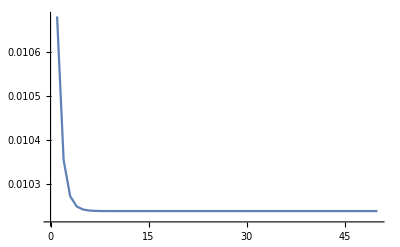

```mathematica
ListLinePlot[half["en"],PlotRange->Full]
```

```mathematica
ailist={{0,0},{-1,2},{-1,1},{-2,3}};
```

```mathematica
aM1={0,-1};
aM2={(√3)/2,-1/2};
```

```mathematica
aM={aM1,aM2}
```

{{0,-1},{(√3)/2,-1/2}}

```mathematica
inner=ailist.aM
```

{{0,0},{√3,0},{(√3)/2,1/2},{(3 √3)/2,1/2}}

```mathematica
halffig=Table[Graphics[{MapThread[{PointSize[#2/10],Point[#1]}&,{inner,half["spinsav"][[i,All,1]]}],MapThread[{Arrowheads[Norm[#2]/10],Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,half["spinsav"][[i,All,3;;4]]}]},AspectRatio->Automatic,Axes->True],{i,50}];
```

```mathematica
ListAnimate[halffig]
```

```mathematica
a1={-2,4}.aM;
```

```mathematica
a2={-2,2}.aM;
```

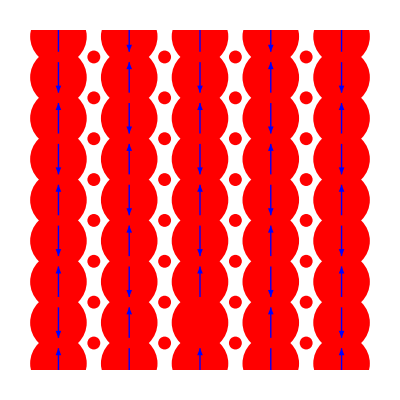

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,half["spinsav"][[-1,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/20],*)Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,half["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,half["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,half["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

-Graphics-

#### 1/3

```mathematica
third=importmat[NotebookDirectory[]<>"nu1,3_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-2,1},{-4,2},{-1,1},{-2,2},{-3,2},{-3,1},{-2,0},{-1,0}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
third["spinsav"][[50]]
```

{{0.876143,0.866698,-0.00039516,0.0000545843},{0.876118,-0.43334,0.750556,0.0000598242},{0.876144,-0.433011,-0.750778,0.0000545229},{0.0619311,-0.00216562,-0.00376404,1.92421×10^-6},{0.0619352,-0.00216701,0.00375056,1.95068×10^-6},{0.0619312,0.00434239,-9.22846×10^-6,1.92451×10^-6},{0.0619312,0.00434239,-6.65448×10^-6,1.92452×10^-6},{0.0619353,-0.00216478,0.00375185,1.95068×10^-6},{0.0619311,-0.00216339,-0.00376532,1.9242×10^-6}}

```mathematica
thirdfig=Table[Graphics[{MapThread[{PointSize[#2/10],Point[#1]}&,{inner,third["spinsav"][[i,All,1]]}],MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,third["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-.5,2},{-.5,3.5}}],{i,50}];
```

```mathematica
ListAnimate[thirdfig]
```

```mathematica
a1={-3,0}.aM;
```

```mathematica
a2={-3,3}.aM;
```

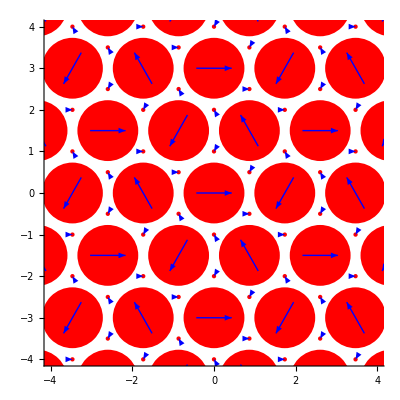

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,third["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,third["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

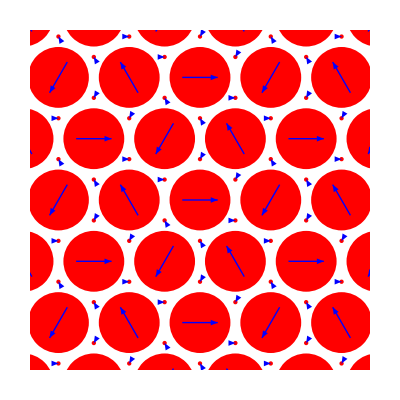

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,third["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,third["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 2/3

```mathematica
twothird=importmat[NotebookDirectory[]<>"nu2,3_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-2,2},{-1,1}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
twothird["spinsav"][[50]]
```

{{0.961737,0.,0.,0.900508},{0.961737,0.,0.,-0.900508},{0.0765263,0.,0.,1.75443×10^-16}}

```mathematica
twothirdfig=Table[Graphics[{MapThread[{PointSize[#2/10],Point[#1]}&,{inner,twothird["spinsav"][[i,All,1]]}],MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,twothird["spinsav"][[i,All,3;;4]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-.5,2},{-.5,2}}],{i,50}];
```

```mathematica
ListAnimate[twothirdfig]
```

```mathematica
a1={-1,2}.aM;
```

```mathematica
a2={-2,1}.aM;
```

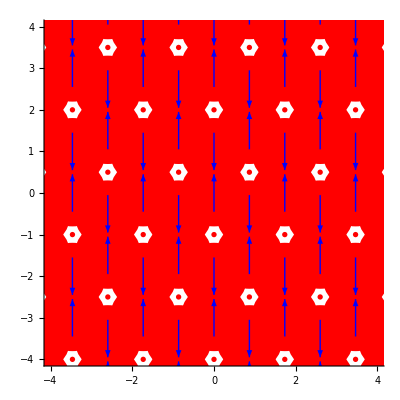

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,twothird["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,twothird["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

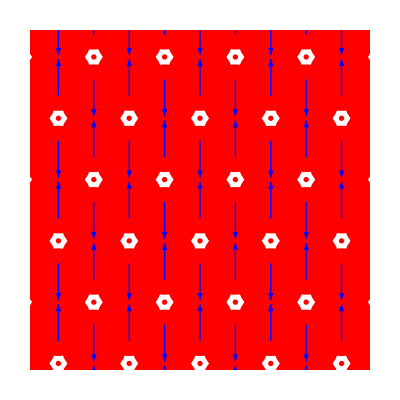

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,twothird["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,twothird["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 1/4

```mathematica
fourth=importmat[NotebookDirectory[]<>"nu1,4_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-2,2},{-4,4},{-1,2},{-2,3},{-3,4},{-1,1},{-3,3},{-5,5},{-2,1},{-3,2},{-4,3}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
fourth["spinsav"][[50]]
```

{{0.595034,0.582628,9.09479×10^-6,-1.30387×10^-6},{0.595033,-0.291325,0.504562,-1.30371×10^-6},{0.595034,-0.291333,-0.504558,-1.40129×10^-6},{0.134983,-0.0545573,2.14727×10^-6,-1.70213×10^-7},{0.134992,0.0272799,0.0472493,-1.79461×10^-7},{0.134982,0.0272776,-0.0472414,-1.67593×10^-7},{0.134991,0.0272794,0.0472498,-1.54406×10^-7},{0.134992,-0.0545618,1.29712×10^-6,-2.65278×10^-7},{0.134994,0.02728,-0.0472483,-2.23887×10^-7},{0.134994,-0.0545632,8.35343×10^-7,-2.10025×10^-7},{0.13498,0.0272749,0.047241,-2.84272×10^-7},{0.134992,0.0272794,-0.0472469,-2.54083×10^-7}}

```mathematica
fourthfig=Table[Graphics[{Red,MapThread[{PointSize[#2/10],Point[#1]}&,{inner,fourth["spinsav"][[i,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,fourth["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-.5,5},{-.5,3.5}}],{i,50}];
```

```mathematica
ListAnimate[fourthfig]
```

```mathematica
a1={-2,4}.aM;
```

```mathematica
a2={-4,2}.aM;
```

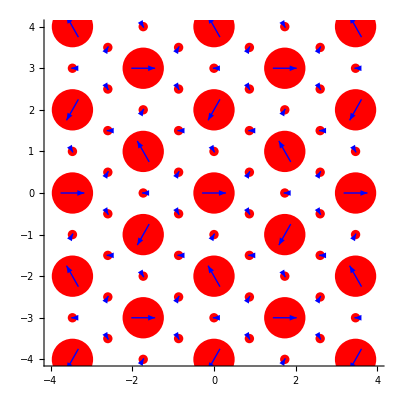

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,fourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,fourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

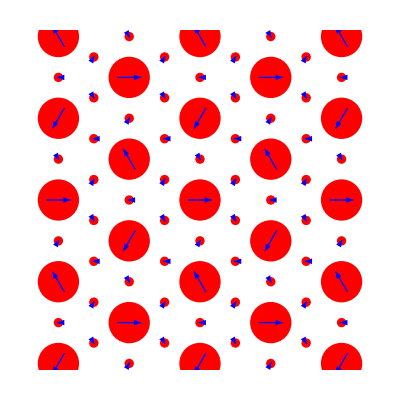

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,fourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,fourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 3/4

```mathematica
threefourth=importmat[NotebookDirectory[]<>"nu3,4_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{0,1},{-1,1},{-1,2}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
threefourth["spinsav"][[50]]
```

{{0.943837,-0.886259,-4.63333×10^-14,-2.47237×10^-14},{0.943801,0.443045,-0.767541,-2.54168×10^-14},{0.943801,0.443045,0.767541,-2.58508×10^-14},{0.168562,9.04061×10^-6,-4.13935×10^-15,1.99813×10^-14}}

```mathematica
threefourthfig=Table[Graphics[{Red,MapThread[{PointSize[#2/10],Point[#1]}&,{inner,threefourth["spinsav"][[i,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,threefourth["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-1,2},{-1.5,1.5}}],{i,50}];
```

```mathematica
ListAnimate[threefourthfig]
```

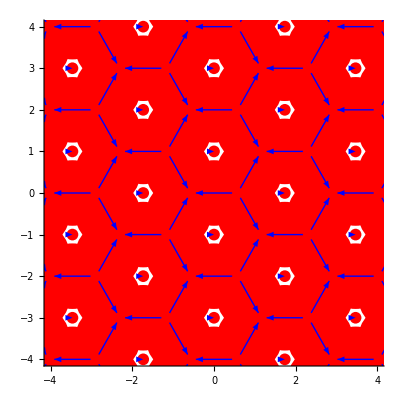

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*2*aM1+j*2*aM2]}&,{inner,threefourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*2aM1+j*2aM2,#1+#2/2+i*2*aM1+j*2*aM2}]}&,{inner,threefourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

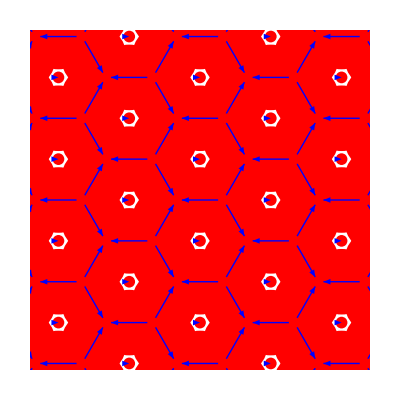

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*2*aM1+j*2*aM2]}&,{inner,threefourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*2aM1+j*2aM2,#1+#2/2+i*2*aM1+j*2*aM2}]}&,{inner,threefourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 1/1

```mathematica
one=importmat[NotebookDirectory[]<>"nu1,1_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-1,1},{-2,2}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
one["spinsav"][[50]]
```

{{1.,0.939912,8.92602×10^-6,1.43109×10^-7},{0.999998,-0.469964,0.81398,1.34756×10^-7},{1.,-0.469973,-0.813978,1.41786×10^-7}}

```mathematica
onefig=Table[Graphics[{Red,MapThread[{PointSize[#2/10],Point[#1]}&,{inner,one["spinsav"][[i,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,one["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-1,2},{-1.5,1.5}}],{i,50}];
```

```mathematica
ListAnimate[onefig]
```

```mathematica
a1={-1,2}.aM;
```

```mathematica
a2={-2,1}.aM;
```

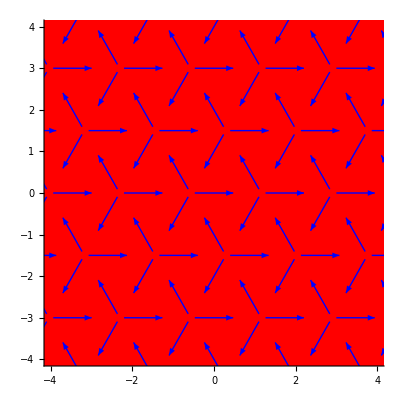

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,one["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,one["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

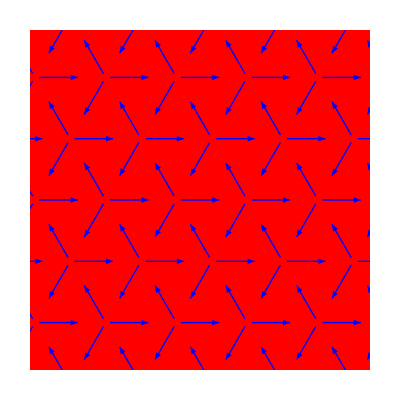

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,one["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,one["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

## Classical energy

```mathematica
shell[n_]:=Block[{a1={0,-1},a2={(√3)/2,-1/2},nshell=n,distsquare,order,shellsorted,break,start,end,shelllist},shelllist=Flatten[Table[{{xindex,yindex},xindex*a1+yindex*a2},{xindex,-nshell,nshell},{yindex,Max[-nshell,-nshell-xindex],Min[nshell-xindex,nshell]}],1];distsquare=Dot[#,#]&/@shelllist[[All,2]];order=Ordering[distsquare];shellsorted=shelllist[[order,2]];break=Flatten[Position[Differences[distsquare[[order]]],_?(#≠0&)]];start=Prepend[break+1,1];end=Append[break,-1];MapThread[shellsorted[[#1;;#2]]&,{start,end}]]
```

```mathematica
nsquare[q_,Ri_,ni_]:=Block[{ν=1/Length[ni]},Abs[Total@MapThread[Exp[-I*q.#1]*#2&,{Ri,ni}]*ν]^2]
```

```mathematica
V[q_,nlist_,Ri_,ni_]:=Block[{n=Length[nlist],U},nsquare[q,Ri,ni]*Sum[Subscript[U,i]*Sum[Exp[I*q.n],{n,nlist[[i]]}],{i,n}]]
```

```mathematica
tot[q_,nlist_,Ri_,ni_]:=Simplify/@Collect[Total@V[q,Rest@nlist,Ri,ni]/2,Subscript[U,_]]
```

```mathematica
neighborlist=shell[8];
```

### U

```mathematica
u=MapThread[#1->#2&,{(Subscript[U,#]&/@Range[5]),{0.1655,0.0886,0.0759,0.0555,0.0482}}]
```

{U_1→0.1655,U_2→0.0886,U_3→0.0759,U_4→0.0555,U_5→0.0482}

### 1/2-rectangular

```mathematica
Qrect={{0,0},{0,2π}};
```

```mathematica
Rlistrect={{0,0},{(√3)/2,-1/2}};
```

```mathematica
occupiedlistrect={1,0};
```

```mathematica
neighborlist=shell[5];
```

```mathematica
rect=tot[Qrect,neighborlist,Rlistrect,occupiedlistrect]
```

U_1/2+U_2/2+(3 U_3)/2+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2

```mathematica
(rect/.u[[1;;#]]&)/@Range[5]
```

{0.08275+U_2/2+(3 U_3)/2+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.12705+(3 U_3)/2+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.2409+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.2964+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.3205+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2}

### 1/2-hexagonal

```mathematica
Rlisthex={{0,0},{-1,0},{0,-1},{1,-1},{1,0},{0,1},{-1,1},{1,1},{0,2},{-1,2},{-2,2},{-2,1}}.{{0,-1},{(√3)/2,-1/2}};
```

```mathematica
Qhex={{-2/3,-1/3},{-1/3,-1/6},{0,0},{1/3,1/6},{2/3,1/3},{1,1/2},{-1/2,0},{-1/6,1/6},{1/6,1/3},{1/2,1/2},{5/6,2/3},{7/6,5/6}}.{{-1/(√3),-1},{2/(√3),0}}*2π;
```

```mathematica
occupiedlisthex={0,1,1,1,1,1,1,0,0,0,0,0};
```

```mathematica
neighborlist=shell[5];
```

```mathematica
hex=tot[Qhex,neighborlist,Rlisthex,occupiedlisthex]
```

U_1/2+U_2+(3 U_3)/4+U_4+U_5+(3 U_6)/2+U_7+(3 U_8)/4+U_9+2 U_10+U_11/2

```mathematica
tot[Qhex,shell[30],Rlisthex,occupiedlisthex]-tot[Qrect,shell[30],Rlistrect,occupiedlistrect]
```

U_2/2-(3 U_3)/4+U_5/2-(3 U_8)/4+U_10+U_12/2-(3 U_13)/2+U_17-(3 U_21)/2+U_22+U_24-(3 U_25)/4+U_28/2-(3 U_29)/2+U_31/2+U_34-(3 U_36)/4+U_40-(3 U_41)/2+U_42-(3 U_44)/2+U_46+(3 U_50)/2-(3 U_51)/2+U_57-(3 U_58)/2+U_61+U_62-(9 U_65)/4+U_67-(3 U_68)/2+U_71+U_73/2+U_76+U_78/2-(3 U_79)/2-(3 U_82)/4-(3 U_84)/2+2 U_86+U_88+U_91-(3 U_92)/2-(3 U_95)/2+U_97-(3 U_99)/2+U_102+U_104+U_109+U_111/2-3 U_112+U_117+U_118-(3 U_119)/2+2 U_121-(3 U_122)/4-(3 U_125)/2+U_126-(3 U_131)/2+(3 U_133)/2-(3 U_135)/2+U_136+U_141-(3 U_144)/4+U_146-(3 U_147)/2+(3 U_149)/2-(3 U_150)/2+U_152+U_155-3 U_157+U_159+U_161-(3 U_163)/2+U_165+U_169-(3 U_172)/2+U_173+U_175-(3 U_176)/2-(3 U_182)/2+U_184+2 U_187-(3 U_188)/2+U_189+U_191+U_193/2-(9 U_194)/4+U_197-(3 U_198)/2-(3 U_200)/2+U_203-(3 U_205)/2+U_206/2+U_209-(3 U_214)/4-(3 U_216)/2+U_217+U_218-(3 U_220)/2

### 2/3

```mathematica
Q={{0,0},{0,4 π/3},{0,-4 π/3}}
```

{{0,0},{0,(4 π)/3},{0,-(4 π)/3}}

```mathematica
Rlist={{0,0},{-1,1},{-2,2}}.{{0,-1},{(√3)/2,-1/2}};
```

```mathematica
occupiedlist={1,0,1};
```

```mathematica
neighborlist=shell[5];
```

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

U_1+2 U_2+U_3+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{0.1655+2 U_2+U_3+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.3427+U_3+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.4186+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.5296+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.626+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11}

### 1/3

```mathematica
occupiedlist={1,0,0};
```

```mathematica
tot[Q,neighborlist,Rlist,occupiedlist]
```

U_2+U_5+U_6+2 U_10

### 1/1

```mathematica
Q={{0,0}};
```

```mathematica
Rlist={{0,0}};
```

```mathematica
occupiedlist={1};
```

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

3 U_1+3 U_2+3 U_3+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{0.4965+3 U_2+3 U_3+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,0.7623+3 U_3+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,0.99+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,1.323+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,1.4676+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11}

### 1/4

```mathematica
Q={{0,0},{1/2,0},{0,1/2},{1/2,1/2}}.{{-1/(√3),-1},{2/(√3),0}}*2π
```

{{0,0},{-π/(√3),-π},{(2 π)/(√3),0},{π/(√3),-π}}

```mathematica
Rlist={{0,0},{0,1},{-1,1},{-1,2}}.{{0,-1},{(√3)/2,-1/2}};
```

```mathematica
occupiedlist={1,0,0,0};
```

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

(3 U_3)/4+(3 U_6)/4+(3 U_8)/4

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{(3 U_3)/4+(3 U_6)/4+(3 U_8)/4,(3 U_3)/4+(3 U_6)/4+(3 U_8)/4,0.056925+(3 U_6)/4+(3 U_8)/4,0.056925+(3 U_6)/4+(3 U_8)/4,0.056925+(3 U_6)/4+(3 U_8)/4}

### 3/4

```mathematica
occupiedlist={1,1,1,0};
```

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

(3 U_1)/2+(3 U_2)/2+(9 U_3)/4+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{0.24825+(3 U_2)/2+(9 U_3)/4+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2,0.38115+(9 U_3)/4+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2,0.551925+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2,0.718425+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2,0.790725+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2}

```mathematica
shellindex[n_]:=Block[{a1={0,-1},a2={(√3)/2,-1/2},nshell=n,distsquare,order,shellsorted,break,start,end,shelllist},shelllist=Flatten[Table[{{xindex,yindex},xindex*a1+yindex*a2},{xindex,-nshell,nshell},{yindex,Max[-nshell,-nshell-xindex],Min[nshell-xindex,nshell]}],1];distsquare=Dot[#,#]&/@shelllist[[All,2]];order=Ordering[distsquare];shellsorted=shelllist[[order,1]];break=Flatten[Position[Differences[distsquare[[order]]],_?(#≠0&)]];start=Prepend[break+1,1];end=Append[break,-1];MapThread[shellsorted[[#1;;#2]]&,{start,end}]]
```